```mathematica
ClearAll["Global`*"]  (*two-stage 2-order TSRK methods (IM-TSRK22)*)
Remove["Global`*"]
ClearAll["p*"]
ClearAll["a*"]
ClearAll["v*"]
ClearAll["w*"]
ClearAll["b*"]
ClearAll["d*"]
nn=3;
e=Table[1,{ii,nn},{i,1}];  e2=Table[1,{ii,nn-1},{i,1}];
v=({{w1*v1, v2+k*a22, v3+k*a23}}); 

A=({{0, 0, 0}, {0, 0, 0}, {w1*a21, a22, a23}});    d=({{1, 0}, {0, 1}, {d31, d32}});   L=({{-w1}, {0}});  b=({{b1+k*d31, b2+d32* k}});
c=A.e+d.L; 
ce=c-e;

C1=DiagonalMatrix[c[[;;,1]]];Ce=DiagonalMatrix[ce[[;;,1]]];
τ2=-((c^2-d.(L^2))/2)+A.c;               τ3=-((c^3-d.(L^3))/6)+A.c^2/2;
τ4=-((c^4-d.(L^4))/4!)+A.c^3/3!;    τ5=-((c^5-d.(L^5))/5!)+A.c^4/4!;
τf2=τ2;   τf3=τ3-τ2;    τf4=τ4-τ3+τ2/2;  τf5=τ5-τ4+τ3/2-τ2/6;
(*τf2=0;   τf3=τ3;    τf4=τ4-τ3;  τf5=τ5-τ4+τ3/2;*)
 p0=1-b.e2;  p1=1-b.L+Total[-v.e,2];    p2=(1-b.(L^2))/2+Total[-v.c,2];
p30=    (1-b.(L^3))/3+Total[-v.c^2 ,2];  pp31=Total[v.τ2,2];
(* d31=0; vv1=0; aa21=a21=0; *)(* w1=1;*)
 a21=0;  a22=0;       v1=v2=v3=0;  d32=1-d31;    c
a23=ad w1+d31 w1; 

a23=((2-√2)/2)w1+d31 w1;  k=10/10;  w1=1;
(*a23=((√3)/3) w1+d31 w1;   k=8/10;  w1=1;*)
c
(*sol=Solve[p0==0&&p1==0&&p2==0,{   b2,b1,d31, b2}]  //FullSimplify *)
sol=Solve[p0==0&&p1==0&&p2==0,{   d31,b1,b2}]  //FullSimplify //N
p0/.sol//FullSimplify   
p1/.sol//FullSimplify      p2/.sol//FullSimplify 
p30/.sol//FullSimplify    
pp31/.sol//FullSimplify
```

{{-w1},{0},{a23-d31 w1}}

{{-1},{0},{1/2 (2-√2)}}

{{d31→0.968311,b1→-0.707107,b2→0.707107}}

{{{0.}}}

{{{0.}}}[{{{1.11022×10^-16}}}]

{{{0.312207}}}

{1.02241}

```mathematica
ClearAll["Global`*"]  (*IM TSRK22  A-stable*)
Remove["Global`*"]
ClearAll["x*"]
ClearAll["y*"]
ClearAll["f*"]
ClearAll["z*"]
(*ad=(√3)/3;bk=8/10; *)
 w1=1;
b2=1-(1+ad) bk+1/w1;
b1=ad bk-1/w1;
d31=(1+w1-ad (1+2 ad) bk w1^2)/((bk+2 ad bk) w1^2);

a23=ad w1+d31 w1;
 d32=1-d31;

ff=b1/k+b2+((d31/k+d32)/(1-a23*z))bk
sol=Solve[ff==k,{ k}]//FullSimplify
```

2-(1+ad) bk+(-1+ad bk)/k+(bk (1-(2-ad (1+2 ad) bk)/(bk+2 ad bk)+(2-ad (1+2 ad) bk)/((bk+2 ad bk) k)))/(1-(ad+(2-ad (1+2 ad) bk)/(bk+2 ad bk)) z)

{{k→((-2+bk) z+ad bk (2+z)-√(bk (bk+2 ad bk z+(-4+(1+ad)^2 bk) z^2)))/(bk+2 ad bk-2 z)},{k→((-2+bk) z+ad bk (2+z)+√(bk (bk+2 ad bk z+(-4+(1+ad)^2 bk) z^2)))/(bk+2 ad bk-2 z)}}

0.841658

0.841658

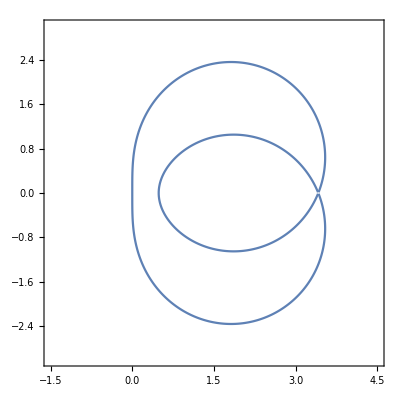

```mathematica
ClearAll["Global`*"]  (*(IM-TSRK22)  A-stable*)
Remove["Global`*"]
ClearAll["x*"]
ClearAll["y*"]
ClearAll["f*"]
ClearAll["z*"]
ad=(√3)/3;bk=8/10; 
ad=(2-√2)/2; bk=10/10; 

z=x+I*y;

f1[z_]:=((-2+bk) z+ad bk (2+z)-√(bk (bk+2 ad bk z+(-4+(1+ad)^2 bk) z^2)))/(bk+2 ad bk-2 z);
f2[z_]:=((-2+bk) z+ad bk (2+z)+√(bk (bk+2 ad bk z+(-4+(1+ad)^2 bk) z^2)))/(bk+2 ad bk-2 z);
 
x=600; y=0.;
Abs[f1[z]]//N    
 Abs[f2[z]]//N

ss1=ContourPlot[N[Abs[f1[z]]]==1.0,{x,-1.5,4.5},{y,-3,3},AspectRatio->1.2,PlotPoints->100] ;
ss2=ContourPlot[N[Abs[f2[z]]]==1.0,{x,-1.5,4.5},{y,-3,3},AspectRatio->1.2,PlotPoints->100] ;
Show[ss1,ss2,AspectRatio->1.0]
```

```mathematica
ClearAll["Global`*"]  (*(IM-TSRK22) A-stable*)
Remove["Global`*"]
ClearAll["z*"]
f1=((-9+2 √3) z+2 √3 (2+√(3+2 √3 z+(-11+2 √3) z^2)))/(6+4 √3-15 z);

f2=(4 √3-9 z+2 √3 z-2 √(9+6 √3 z+(-33+6 √3) z^2))/(6+4 √3-15 z);
lim_(z->-∞) f1//Abs
lim_(z->∞) f1//Abs//N
lim_(z->-∞) f2//Abs//N
lim_(z->∞) f2//Abs//N
```

1/15 √(4 (33-6 √3)+(9-2 √3)^2)

0.733566

0.733566

0.733566